### Impotering af billeder og resize

```mathematica
filepath:=SystemDialogInput["FileOpen",WindowTitle->"Select a Image to Open"]
userimage =ImageResize[Import[filepath],500];
```

### Justering af EdgeDetect

```mathematica
Manipulate[
edge:=DeleteSmallComponents[EdgeDetect[userimage,1,kontrast],sc];
DeleteSmallComponents[EdgeDetect[userimage,1,kontrast],sc]

,{{sc,20,"Delete Small Components"},0,50},{{kontrast,0.05,"Kontrast"},0,0.1}]
```

### Finder hvide pixsler og indsetter dem i rekkeføge i en liste

```mathematica
poss:=PixelValuePositions[edge,1];
route=FindShortestTour[poss][[2]];
possroute=Append[poss[[route]],poss[[route]][[2]]];
```

### Scaling and Transforming

```mathematica
scale=100;
max=x/.Solve[Max[possroute]/x==scale,x][[1]];
For[i=1,i≤  Length[possroute],i++,
possroute[[i]]={(possroute[[i]][[1]])/max//N,(possroute[[i]][[2]])/max//N};
]
For[i=1,i≤  Length[possroute],i++,
possroute[[i]]={possroute[[i]][[1]]-((ImageDimensions[userimage][[1]])/max)/2,possroute[[i]][[2]]-((ImageDimensions[userimage][[2]])/max)/2}
]
```

### Viser et previw af ruten

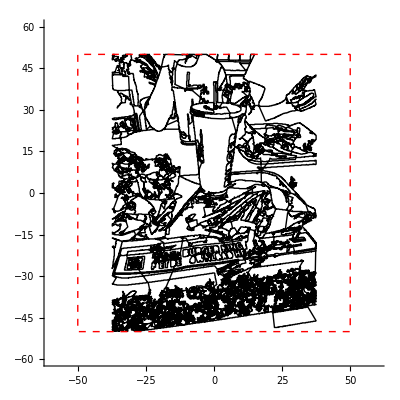

```mathematica
box={{50,50},{50,-50},{-50,-50},{-50,50},{50,50}};
Show[Graphics[Line[possroute],Axes->True,PlotRange->{{-60,60},{-60,60}}],
Graphics[{Dashed,Red,Line[box]},Axes->True,PlotRange->{{-60,60},{-60,60}}]]
```

### Tjekker for om distangsen mellem punkterne er mere end qrt[(1/max)^2+(1/max)^2] af hindanden, laver dem til travellines og indsætter i en ny liste

```mathematica
travel:=Table[EuclideanDistance[possroute[[i]],possroute[[i+1]]],{i,1,Length[possroute]-1}]
maxlength=500;
trtotal=0;
isoroute={};
maxtravel=Sqrt[(1/max)^2+(1/max)^2];
For[i=1,i≤  Length[possroute]-1,i++,
If[travel[[i]]>maxtravel,
AppendTo[isoroute,Flatten[{possroute[[i]],00,10}]];
AppendTo[isoroute,Flatten[{possroute[[i+1]],00,10}]],
AppendTo[isoroute,Flatten[{possroute[[i+1]],01,-0.5}]];
trtotal=trtotal+EuclideanDistance[possroute[[i]],possroute[[i+1]]];
If[trtotal≥maxlength,
AppendTo[isoroute,Insert[Insert[{0,0},98,3],-30,4]];trtotal=0;
AppendTo[isoroute,isoroute[[Length[isoroute]-1]]]
]
];
]
```

### indsætter codinater som gcode i en fil og expoter

```mathematica
file=CreateFile[];
Table[
If[ToString[isoroute[[i]][[3]]]=="98",
WriteLine[file,
"N"<>ToString[i]<>
" G"<>ToString[isoroute[[i]][[3]]]<>
" Z"<>ToString[isoroute[[i]][[4]]]
]
,
WriteLine[file,
"N"<>ToString[i]<>
" G"<>ToString[isoroute[[i]][[3]]]<>
" X"<>ToString[isoroute[[i]][[1]]]<>
" Y"<>ToString[isoroute[[i]][[2]]]<>
" Z"<>ToString[isoroute[[i]][[4]]]
]
]
,{i,1,Length[isoroute]}];

ex:=SystemDialogInput["FileSave",WindowTitle->"Select a Image to Open"]
CopyFile[file,ex<>".nc"];
```